```mathematica
Clear[A, Γ, x, c]
A=1;
Γ=1;
Integrate[(A*Γ)/(2*Pi*((x)^2+(Γ/2)^2)), {x, -Infinity,Infinity }]
Integrate[Sqrt[(A*Γ)/(2*Pi*((x)^2+(Γ/2)^2))], {x, -1/2,1/2}]
Integrate[Sqrt[(A*Γ)/(2*Pi*((x)^2+(Γ/2)^2))], {x, -1,1}]
Integrate[Sqrt[(A*Γ)/(2*Pi*((x)^2+(Γ/2)^2))], {x, -10,10}]
N[Sqrt[2/Pi]*ArcSinh[1],6]
Print["ArcSinh[2] = ",N[ArcSinh[2],6]]
N[Sqrt[2/Pi]*ArcSinh[20],6]
N[Sqrt[2/Pi],6]
```

1

√(2/π) ArcSinh[1]

√(2/π) ArcSinh[2]

√(2/π) ArcSinh[20]

0.703234

ArcSinh[2] = 1.44364

2.9438

0.797885

```mathematica
io
```

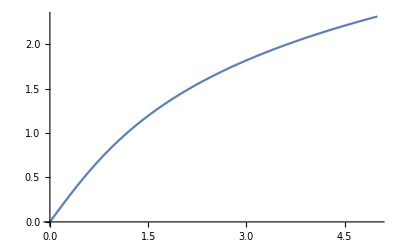

```mathematica
Plot[ArcSinh[x],{x,0.01, 5}]
```